```mathematica
DD[ k_, a_, n_ ] := Sum[(-1)^(j+1) Binomial[k,j] DD[ k-j, m, Floor[n/(m^j)]], {m,a, n^(1/k)},{j,1,k}]
DD[ 1,a_, n_ ]:= Floor[n]-a+1
DD[0,a_,n_] := 1
DS[ n_, k_ ] := DD[k,2,n]
DDD[n_, k_ ] := Sum[ DDD[n/j, k-1],{j,2,n}]
DDD[n_,0] := 1
```

```mathematica
DD[3,2,1000]
```

11217

```mathematica
DDD[1000,3]
```

11217

```mathematica
DS[n,1]
```

-1+Floor[n]

```mathematica
D2a[n_] := Sum[ Binomial[3,2](Sum[Binomial[2,1]Binomial[1,0]Sum[1,{m,j,Floor[(n/(j k))]}]-Binomial[2,0],{j,k,Floor[(n/k)^(1/2)]}]) - Binomial[3,1](Sum[1,{m,k,Floor[n/(k^2)]}]) + Binomial[3,0], {k,2,Floor[n^(1/3)]}]
```

```mathematica
D2a[1000]
```

11217

```mathematica
D2a[n]
```

$Aborted

```mathematica
DS[1000]
```

DS[1000]

```mathematica
D2[n_] := Sum[ Binomial[2,1](Floor[n/m]-m+1) -Binomial[2,0],{m,2,Floor[n^(1/2)]}]
```

```mathematica
D2[n]
```

```mathematica
D3[n_]:=∑_(m=2)^Floor[√n] (-1+2 (1-m+Floor[n/m]))
```

```mathematica
Expand[-1+2 (1-m+Floor[n/m])]
```

1-2 m+2 Floor[n/m]

```mathematica
∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
∑_(m=2)^Floor[√n] 1+∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] 2 Floor[n/m]
```

1-Floor[√n]^2+∑_(m=2)^Floor[√n] 2 Floor[n/m]

```mathematica
D3a[n_]:=∑_(m=2)^Floor[√n] (1-2 m+2 Floor[n/m])
```

```mathematica
D3[n_]:=∑_(m=2)^Floor[√n] 1 +∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] (2 Floor[n/m])
```

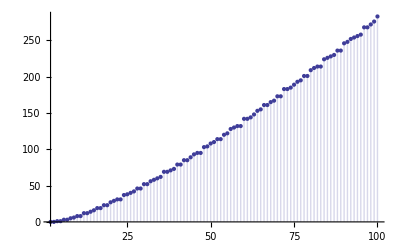

```mathematica
DiscretePlot[D3[n],{n,2,100}]
```

```mathematica
D3[1000]
```

5070

```mathematica
FullSimplify[ ∑_(m=2)^Floor[√n] 1 +∑_(m=2)^Floor[√n] -2 m+∑_(m=2)^Floor[√n] (2 Floor[n/m]) ]
```

1-Floor[√n]^2+∑_(m=2)^Floor[√n] 2 Floor[n/m]

```mathematica
D4[n_] := 1-Floor[√n]^2+2∑_(m=2)^Floor[√n] Floor[n/m]
```

```mathematica
DiscretePlot[D4[n],{n,2,100}]
```

-Graphics-

```mathematica
D4[1000]
```

5070